```mathematica
u= {{1/2,1/2,0},{1/2,1/2,0},{0,0,1}};
P = KroneckerProduct[u,u];
p2= 0;
pd2 = 0;
A={{1,0,0,0,0,0,0,0,0},(*00*){0,1-p2,p2,0,0,0,0,0,0},(*01*){0,p2,1-p2-pd1,0,pd1,0,0,0,0},(*02*){0,0,0,1-p1,0,0,p1,0,0},(*10*){0,0,pd1,0,1-p1-p2-pd1-pd2,p2,pd2,p1,0},(*11*){0,0,0,0,p2,1-p1-p2-pd3,0,pd3,p1},(*12*){0,0,0,p1,pd2,0,1-p1-pd2,0,0},(*20*){0,0,0,0,p1,pd3,0,1-p1-p2-pd3,p2},(*21*){0,0,0,0,0,p1,0,p2,1-p1-p2}};(*22*)
Smat = Dot[P,A];
```

```mathematica
Simplify[Eigenvalues[Smat]]
```

{1,0,0,0,0,0,1/4 Root[-64+192 p1-144 p1^2+48 pd1-120 p1 pd1+72 p1^2 pd1+64 pd3-144 p1 pd3+72 p1^2 pd3-32 pd1 pd3+36 p1 pd1 pd3+(48-96 p1+36 p1^2-24 pd1+30 p1 pd1-32 pd3+36 p1 pd3+8 pd1 pd3) #1+(-12+12 p1+3 pd1+4 pd3) #1^2+#1^3&,1],1/4 Root[-64+192 p1-144 p1^2+48 pd1-120 p1 pd1+72 p1^2 pd1+64 pd3-144 p1 pd3+72 p1^2 pd3-32 pd1 pd3+36 p1 pd1 pd3+(48-96 p1+36 p1^2-24 pd1+30 p1 pd1-32 pd3+36 p1 pd3+8 pd1 pd3) #1+(-12+12 p1+3 pd1+4 pd3) #1^2+#1^3&,2],1/4 Root[-64+192 p1-144 p1^2+48 pd1-120 p1 pd1+72 p1^2 pd1+64 pd3-144 p1 pd3+72 p1^2 pd3-32 pd1 pd3+36 p1 pd1 pd3+(48-96 p1+36 p1^2-24 pd1+30 p1 pd1-32 pd3+36 p1 pd3+8 pd1 pd3) #1+(-12+12 p1+3 pd1+4 pd3) #1^2+#1^3&,3]}

```mathematica
{vals, vecs} = Eigensystem[Smat];
```

```mathematica
Dot[vecs[[7]], vec[8]]
```

{-pd1+((-pd1+pd1 pd2) (-3+pd1+pd2+Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]) (-4+2 pd1+2 pd3+Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]))/(pd1 (-4 pd2+2 pd1 pd2+2 pd1 pd3+2 pd2 pd3+pd2 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]))-((-3+pd1+pd2+Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]) (-4+2 pd1+2 pd3+Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]) (2 pd1-2 pd1 pd3-2 pd2 pd3-pd1 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]))/(2 pd1 (-4 pd2+2 pd1 pd2+2 pd1 pd3+2 pd2 pd3+pd2 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]))-1/pd1(-3 pd3+pd1 pd3+pd2 pd3+pd3 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]),-pd3/pd1+((-1+pd2) (-4+2 pd1+2 pd3+Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]))/(-4 pd2+2 pd1 pd2+2 pd1 pd3+2 pd2 pd3+pd2 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1])+((4-2 pd1-2 pd3-Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]) (2 pd1-2 pd1 pd3-2 pd2 pd3-pd1 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]))/(2 pd1 (-4 pd2+2 pd1 pd2+2 pd1 pd3+2 pd2 pd3+pd2 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1])),-((4 pd1-2 pd1 pd2-2 pd1 pd3-2 pd2 pd3-pd1 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1])/(-4 pd2+2 pd1 pd2+2 pd1 pd3+2 pd2 pd3+pd2 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1])),-pd3/pd1+((-1+pd2) (-4+2 pd1+2 pd3+Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]))/(-4 pd2+2 pd1 pd2+2 pd1 pd3+2 pd2 pd3+pd2 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1])+((4-2 pd1-2 pd3-Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]) (2 pd1-2 pd1 pd3-2 pd2 pd3-pd1 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]))/(2 pd1 (-4 pd2+2 pd1 pd2+2 pd1 pd3+2 pd2 pd3+pd2 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1])),-pd3/pd1+((-1+pd2) (-4+2 pd1+2 pd3+Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]))/(-4 pd2+2 pd1 pd2+2 pd1 pd3+2 pd2 pd3+pd2 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1])+((4-2 pd1-2 pd3-Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]) (2 pd1-2 pd1 pd3-2 pd2 pd3-pd1 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1]))/(2 pd1 (-4 pd2+2 pd1 pd2+2 pd1 pd3+2 pd2 pd3+pd2 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1])),-((4 pd1-2 pd1 pd2-2 pd1 pd3-2 pd2 pd3-pd1 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1])/(-4 pd2+2 pd1 pd2+2 pd1 pd3+2 pd2 pd3+pd2 Root[-64+48 pd1-8 pd1^2+48 pd2-24 pd1 pd2-8 pd2^2+4 pd1 pd2^2+64 pd3-32 pd1 pd3-32 pd2 pd3+4 pd1 pd2 pd3+4 pd2^2 pd3+(48-24 pd1+2 pd1^2-24 pd2+6 pd1 pd2+2 pd2^2-32 pd3+8 pd1 pd3+8 pd2 pd3) #1+(-12+3 pd1+3 pd2+4 pd3) #1^2+#1^3&,1])),1,1,0}.vec[8]

```mathematica
Clear[pd2]
```

```mathematica
u= {{1/2,1/2,0},{1/2,1/2,0},{0,0,1}};
P = KroneckerProduct[u,u];
p1 = p2;
pd2 = 0;
pd3=0;
A={{1,0,0,0,0,0,0,0,0},(*00*){0,1-p2,p2,0,0,0,0,0,0},(*01*){0,p2,1-p2-pd1,0,pd1,0,0,0,0},(*02*){0,0,0,1-p1,0,0,p1,0,0},(*10*){0,0,pd1,0,1-p1-p2-pd1-pd2,p2,pd2,p1,0},(*11*){0,0,0,0,p2,1-p1-p2-pd3,0,pd3,p1},(*12*){0,0,0,p1,pd2,0,1-p1-pd2,0,0},(*20*){0,0,0,0,p1,pd3,0,1-p1-p2-pd3,p2},(*21*){0,0,0,0,0,p1,0,p2,1-p1-p2}};(*22*)
Smat = Dot[P,A];
```

```mathematica
{vals, vecs} = Eigensystem[Smat];
```

```mathematica
vals
```

{1,0,0,0,0,0,1/2 (2-3 p2-pd1),1/4 (4-9 p2-2 pd1-√(9 p2^2+4 pd1^2)),1/4 (4-9 p2-2 pd1+√(9 p2^2+4 pd1^2))}

```mathematica
Dot[vecs[[8]], vec[[9]]]
```

Part::partd: Part specification vec⟦9⟧ is longer than depth of object.

{(-32 p1 p2+48 p1^2 p2-32 p1 pd3+48 p1^2 pd3+32 p2 pd3+30+1-6 p1^2 1^2-10 p1 p2 Root[1&,2]^2-2 p1 pd1 Root[-64+31+#1^3&,2]^2-4 p1 pd3 Root[-64+31+#1^3&,2]^2-p1 Root[-64+192 p1-144 p1^2+27+(-12+12 p1+12 p2+3 pd1+4 pd3) #1^2+#1^3&,2]^3)/(8 (-16 p2+32 p1 p2-12 p1^2 p2+34+2 p1 p2 pd3 Root[-64+192 p1-144 p1^2+27+(-12+12 p1+12 p2+3 pd1+4 pd3) #1^2+#1^3&,2]-p2 Root[-64+31+#1^3&,2]^2+p1 p2 Root[-64+192 p1-144 p1^2+27+(-12+12 p1+12 p2+3 pd1+4 pd3) #1^2+#1^3&,2]^2)),1/(8 (1)),5,-1/(4 1),1}.1
 |  |  |  |

```mathematica
Clear[p1,p2,pd1,pd2,pd3]
```

```mathematica
pd3 = 8.25*10^(-4)-3/4*pd1;
```

```mathematica
a1 = (7*(pd1-1/2000)^2+2*(2*pd3-1/2000)^2+2*(pd1-2*pd3)^2)^(1/2);
```

```mathematica
fv=Simplify[a1^2-(8 * 2.24*10^(-4))^2]
```

24. (2.76197×10^-7-0.00126667 pd1+pd1^2)

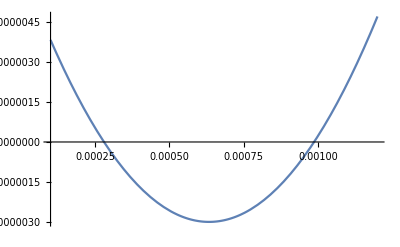

```mathematica
Plot[fv,{pd1,0.0001,0.0012}]
```

```mathematica
f[pd1_]:=24. (2.761973333333333*^-7-0.0012666666666666666 pd1+pd1^2)
```

```mathematica
Solve[4. (2.761973333333333*^-7-0.0012666666666666666 pd1+pd1^2)==0,pd1]
```

{{pd1→0.000279902},{pd1→0.000986765}}

```mathematica
0.0002799019004106548+0.0009867647662560118
```

```mathematica
0.0012666666666666666/2
```

0.000633333

```mathematica
8.25*10^(-4)-3/4*0.0002799019004106548
```

0.000615074

```mathematica
8.25*10^(-4)-3/4*0.0009867647662560118
```

0.0000849264